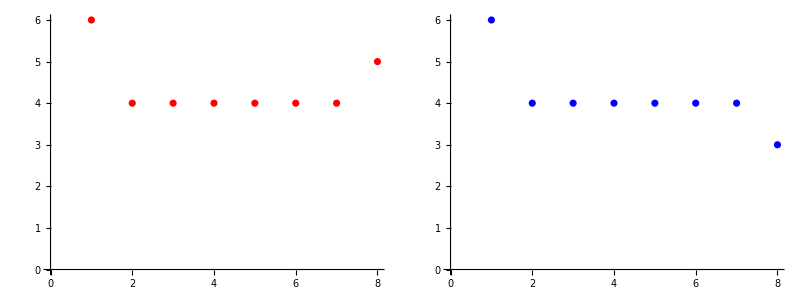

```mathematica
plt1= ListPlot[{6, 4, 4, 4, 4, 4, 4, 5}, PlotStyle-> Red, PlotRange -> All, AxesOrigin->{0,0}, BaseStyle->{FontSize->12}];
plt2 = ListPlot[{6, 4, 4, 4, 4, 4, 4, 3}, PlotStyle-> Blue, PlotRange -> All, AxesOrigin->{0,0}, BaseStyle->{FontSize->12}];
grid= Grid[{{plt1, plt2}}]
```

```mathematica
Export["UU//Template//figures//valleyplateau.pdf", grid]
```

UU//Template//figures//valleyplateau.pdf